```mathematica
Global Conditions
```

Conditions Global

```mathematica
Clear["Global`*"]
e1=0.01;
e2=0.05;
r=3;
ϵ=(1-e1)*(1-e2)+e1*e2;
ϵ=.9802
e=e2;
(*ternary coords where x corresponds to freq alld, y to freq allc *)
TernCoords[x_,y_]={{1/2,-1/2},{-Tan[Pi/3]/2,-Tan[Pi/3]/2}}.{x,y}+{1/2,Tan[Pi/3]/2};
diskradius=.015;
textoffset=.05;
thickness=.005;
vlabels={Graphics[Text["AllD",{-textoffset,-textoffset}]],Graphics[Text["AllC",{1+textoffset,-textoffset}]],Graphics[Text["Disc",{1/2,Tan[Pi/3]/2+textoffset}]]};
SetDirectory["/Users/brycemorsky/Desktop/New projects/Indirect reciprocity/figures"];
```

```mathematica
(* Scoring *)
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=Pcg;
Pdb=Pdg;
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg-gx[t],
gy'[t]==Qdg-gy[t],
gz'[t]==Qcg*g+Qdg*(1-g)-gz[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{gx,gy,gz},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);
(* Equilibria *)
fullsys={
x'[t]==(x*(pix-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
y'[t]==(y*(piy-pi)/.{x->x[t],y->y[t],gx->gx[t],gy->gy[t],gz->gz[t]}),
gx'[t]==(100*(Qcg-gx[t])/.{x->x[t],y->y[t]}),
gy'[t]==(100*(Qdg-gy[t])/.{x->x[t],y->y[t]}),
gz'[t]==(100*(Qcg*g+Qdg*(1-g)-gz[t])/.{x->x[t],y->y[t]})
};
Eq=Array[m,{81,2}];
count = 1;
(*Do[
R=NDSolve[Join[fullsys,{x[0]==0.0125*i,y[0]==0.0125*j,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,1000},Method->"StiffnessSwitching"];
Eq[[count]]= {x[1000]/.R[[1]],y[1000]/.R[[1]]};
count=count+1;
,{i,1,79},{j,1,80-i}];*)
Do[
R=NDSolve[Join[fullsys,{x[0]==0.00402*i,y[0]==0.00402*i,gx[0]==0.5,gy[0]==0.5,gz[0]==0.5}],{x,y,gx,gy,gz},{t,0,100000},Method->"StiffnessSwitching"];
Eq[[count]]= {x[100000]/.R[[1]],y[100000]/.R[[1]]};
count=count+1;
,{i,0,80}];
dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius],EdgeForm[Blue],White,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@Join[Eq,{{0.32295466114708093,0.32295466114708093}}]]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0.32295466114708093,0.32295466114708093],diskradius]}],
Graphics[{White,Disk[TernCoords[0.32295466114708093,0.32295466114708093],diskradius-thickness/2,{Pi/2,3*Pi/2}]}]
};
(*dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius],EdgeForm[Blue],White,Line[TernCoords[#1,#2]&@@@{{0,0},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@{{0,1},{0,0.66}}]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[TernCoords[#1,#2]&@@@Join[Eq,{{0,0.66}}]]}]
};*)
(*Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[#1,#2],diskradius]}]&@@@Eq*)
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageScBayes=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["Sc_Bayes.pdf",imageScBayes];
```

```mathematica
(* Shunning Bayes *)
Print["Shunning Bayes"];

pix=r*x-1;
piy=r*x;
piz=r*x;
pi=x*pix+y*piy+z*piz;

xdot[x_,y_,z_]=x*(pix-pi);
ydot[x_,y_,z_]=y*(piy-pi);
zdot[x_,y_,z_]=z*(piz-pi);

vx=xdot[x,y,1-y-x];
vy=ydot[x,y,1-y-x];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[{TernCoords[0,0],TernCoords[0,1]}]}]
};

dp=StreamPlot[{vx,vy},{x,0,1},{y,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageShBayes=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["Sh_Bayes.pdf",imageShBayes];
```

Shunning Bayes

```mathematica
(* Simple standing *)
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g+1-g-gx[t],
gy'[t]==Qdg*g+1-g-gy[t],
gz'[t]==Qcg*g2+Qdg*(g-g2)+1-g-gz[t],
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[{TernCoords[0,0],TernCoords[0.5,0]}]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0.646,0],diskradius]}]
};

dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSBayes=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["SS_Bayes.pdf",imageSSBayes];
```

```mathematica
(* Staying *)
g=x*gx[t]+y*gy[t]+(1-x-y)*gz[t];
g2=x*gx2[t]+y*gy2[t]+(1-x-y)*gz2[t];
Pcg=ϵ*g/(ϵ*g+e*(1-g));
Pdg=(1-ϵ)*g/((1-ϵ)*g+(1-e)*(1-g));
Pcb=e*g/(e*g+ϵ*(1-g));
Pdb=(1-e)*g/((1-e)*g+(1-ϵ)*(1-g));
Qcg=ϵ*Pcg+(1-ϵ)*Pdg;
Qdg=(1-e)*Pdg+e*Pcg;
Qcb=ϵ*Pcb+(1-ϵ)*Pdb;
Qdb=(1-e)*Pdb+e*Pcb;
repsys={
gx'[t]==Qcg*g-g*gx[t],
gy'[t]==Qdg*g-g*gy[t],
gz'[t]==(Qcg-Qdg)*g2+Qdg*g-g*gz[t],
gx2'[t]==gx[t]^2-gx2[t],
gy2'[t]==gy[t]^2-gy2[t],
gz2'[t]==gz[t]^2-gz2[t]
};
M=Array[m,{66,5}];
count=1;
Do[
R=NDSolve[Join[repsys/.{x->0.1*i,y->0.1*j},{gx[0]==0.5,gy[0]==0.5,gz[0]==0.5,gx2[0]==0.25,gy2[0]==0.25,gz2[0]==0.25}],{gx,gy,gz,gx2,gy2,gz2},{t,0,100}];
M[[count]]= {0.1*i,0.1*j,gx[100]/.R[[1]],gy[100]/.R[[1]],gz[100]/.R[[1]]};
count=count+1;
,{i,0,10},{j,0,10-i}];
pix=r*(x+gx*(1-x-y))-1;
piy=r*(x+gy*(1-x-y));
piz=r*(x+gz*(1-x-y))-(gx*x+gy*y+gz*(1-x-y));
pi=x*pix+y*piy+(1-x-y)*piz;
xdot=x*(pix-pi);
ydot=y*(piy-pi);
vdata={x,y,xdot,ydot}/.(Thread[{x,y,gx,gy,gz}->#]&/@M);

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0.33,0],diskradius]}]
};
(*Graphics[{EdgeForm[Thickness[thickness]],CapForm["Round"],Thickness[diskradius+thickness*2],EdgeForm[Blue],Blue,Line[{TernCoords[0,0],TernCoords[0.5,0]}]}],*)
dp=ListStreamPlot[Partition[#,2]&/@vdata,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageStBayes=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["St_Bayes.pdf",imageStBayes];
```

```mathematica
(* Stern judging Bayes and non-Bayes *)
Print["Stern judging"];

pix=r*(x+0.5*z)-1;
piy=r*(x+0.5*z);
piz=r*(x+0.5*z)-0.5;
pi=x*pix+y*piy+z*piz;

xdot[x_,y_,z_]=x*(pix-pi);
ydot[x_,y_,z_]=y*(piy-pi);
zdot[x_,y_,z_]=z*(piz-pi);

vx=xdot[x,y,1-y-x];
vy=ydot[x,y,1-y-x];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};
TernCoords[0,0]
dp=StreamPlot[{vx,vy},{x,0,1},{y,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJ=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["SJ.pdf",imageSJ];
```

Stern judging

```mathematica
Print["Scoring Strict"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==ep^Q,gy==e2^Q,gz==(g ep+(1-g) e2)^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[1]][[2,2]],equillibria[[1]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCStrict.pdf",imageSCStrict];

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSCStrict-vector.pdf",ternplot];
```

```mathematica
equillibria[[1]][[2,2]]
```

-1.60896

```mathematica
Print["Scoring Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-ep)^Q,gy==1-(1-e2)^Q,gz==1-(1-(g ep+(1-g) e2))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[2]];
piy=b (fx+fz gy) (1-e1)/.soln[[2]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[2]];
pi=fx pix+fy piy+fz piz/.soln[[2]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria-- this computes fine but gives diff restults than origi submission*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]
(*equil at DISC only b/c blowup at ALLD,but ALLD is an equil:*)
(*
{vx,vy}/.{fx->0,fy->1}
{vx,vy}/.{fx->0,fy->.9999}
{vx,vy}/.{fx->0,fy->.9}
*)

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[1]][[2,2]],equillibria[[1]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCTol.pdf",imageSCTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None,VectorPoints->30];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSCTol-vector.pdf",ternplot]
```

Scoring Tolerant

$Aborted

Part::partd: Part specification equillibria⟦1⟧ is longer than depth of object.

Part::partd: Part specification equillibria⟦1⟧⟦2,2⟧ is longer than depth of object.

Part::partd: Part specification equillibria⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

ReplaceAll::reps: {cond} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

imageSCTol.pdf

ReplaceAll::reps: {cond} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

imageSCTol-vector.pdf

```mathematica
equillibria
```

ReplaceAll::reps: {cond} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1-e1^2-2 e1 e2+4 e1^2 e2-e2^2+4 e1 e2^2-4 e1^2 e2^2,2 e2-e2^2,-2. (0.3-0.3 e1^2+0.4 e2-0.6 e1 e2+1.2 e1^2 e2-0.5 e2^2+1.2 e1 e2^2-1.2 e1^2 e2^2+(0.5 e1)/(0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)+(1.5 e2)/(0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)-(1.5 e1 e2)/(0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)-(1. e2^2)/(0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)+(1. e1 e2^2)/(0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)-(√((0.+1. e1+3. e2-3. e1 e2-2. e2^2+2. e1 e2^2)^2-4 (-0.3+0.3 e1^2-1.4 e2+0.6 e1 e2-1.2 e1^2 e2+1. e2^2-1.2 e1 e2^2+1.2 e1^2 e2^2) (0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)))/(2 (0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2))),(0.-1. e1-3. e2+3. e1 e2+2. e2^2-2. e1 e2^2+√((0.+1. e1+3. e2-3. e1 e2-2. e2^2+2. e1 e2^2)^2-4 (-0.3+0.3 e1^2-1.4 e2+0.6 e1 e2-1.2 e1^2 e2+1. e2^2-1.2 e1 e2^2+1.2 e1^2 e2^2) (0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2)))/(2 (0.5-1. e1+0.5 e1^2-2. e2+4. e1 e2-2. e1^2 e2+2. e2^2-4. e1 e2^2+2. e1^2 e2^2))}/.cond

ReplaceAll::reps: {cond} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
Print["Scoring E=0 no institution"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==ep,
gy==e2,
gz==g ep+(1-g)e2,
g==fx gx+fy gy+fz gz
},
{gx,gy,gz,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

otherequil=FindRoot[Evaluate[vy] /. fx->0,{fy,.75}][[1,2]]
{vx,vy} /. {fx->0,fy->.787415}

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

otherdots=Table[
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[ep,FindRoot[Evaluate[vy] /. fx->ep,{fy,.75}][[1,2]]],diskradius]}]
,{ep,0,.787,.03}];

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSCE0=Show[ternplot,dots,otherdots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSCE0.pdf",imageSCE0]
```

Scoring E=0 no institution

{0.9608,0.02,0.55691,0.570695}

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -(92291 fx)/87992-(121001 fy)/175984 == 1.

{{fx→-4.2664,fy→5.05382}}

0.787415

{0.,6.56179×10^-10}

imageSCE0.pdf

```mathematica
Print["SS Strict"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==(g ep+(1-g)(1-e2))^Q,gy==(g e2+(1-g)(1-e2))^Q,gz==(g ep+(1-g)(1-e2))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[5]][[1,2]],equillibria[[5]][[2,2]]],diskradius]}]
};


dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSStrict.pdf",imageSSStrict];

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];

Export["imageSSStrict-vector.pdf",ternplot]
```

SS Strict

{0.932074,0.0634924,0.932074,0.758357}

{{fx→1.,fy→-2.72635×10^-10},{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→0,fy→0.862886},{fx→0,fy→1.},{fx→0,fy→1.}}

imageSSStrict-vector.pdf

```mathematica
Print["SS Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-(g ep+(1-g)(1-e2)))^Q,gy==1-(1-(g e2+(1-g)(1-e2)))^Q,gz==1-(1-(g ep+(1-g)(1-e2)))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

soln2simple=FullSimplify[soln[[2]],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln2simple;
piy=b (fx+fz gy) (1-e1)/.soln2simple;
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln2simple;
pi=fx pix+fy piy+fz piz/.soln2simple;

fxdot[fx_,fy_,fz_]=Simplify[fx (pix-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
fydot[fx_,fy_,fz_]=Simplify[fy (piy-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
fzdot[fx_,fy_,fz_]=Simplify[fz (piz-pi),{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];

(*
vxanalytic=Simplify[fxdot[fx,fy,1-fy-fx],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
vyanalytic=Simplify[fydot[fx,fy,1-fy-fx],{e1>0,e1<1,e2>0,e2<1,fx>0,fx<1,fy>0,fy<1,fx+fy<1,b>0,c>0,b>c}];
 Solve[{vxanalytic==0,vyanalytic==0},{fx,fy}]
*)

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[11]][[1,2]],equillibria[[11]][[2,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSTol.pdf",imageSSTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSSTolt-vector.pdf",ternplot]
```

SS Tolerant

{0.998671,0.289943,0.998671,0.856926}

{{fx→0.0000521364-0.000658821 ⅈ,fy→-0.000344444-0.0000639353 ⅈ},{fx→0.0000521307-0.000658823 ⅈ,fy→-0.000344445-0.0000639329 ⅈ},{fx→-0.000218715-0.000811746 ⅈ,fy→-0.000449456+0.0000838497 ⅈ},{fx→-0.000218725-0.000811745 ⅈ,fy→-0.000449456+0.000083853 ⅈ},{fx→1.,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→0.699492},{fx→0,fy→0.699492}}

imageSSTol.pdf

imageSSTolt-vector.pdf

```mathematica
Print["SS E=0 no institution"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==g ep+(1-g)(1- e2),
gy==g e2 + (1-g)(1-e2),
gz==(g2 ep+ d2 + b2(1- e2)),
g==fx gx+fy gy+fz gz,
g2==fx gx^2+fy gy^2+fz gz^2,
b2 == 1 -2 g + g2,
d2 == (g-g2)
},
{gx,gy,gz,g2,b2,d2,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[equillibria[[4]][[2,2]],equillibria[[4]][[1,2]]],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[11]][[2,2]],equillibria[[11]][[1,2]]],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSSE0=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSSE0.pdf",imageSSE0]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSSE0-vector.pdf",ternplot]
```

SS E=0 no institution

{0.965194,0.239709,0.867272,0.771136}

{{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}}

Part::partw: Part 11 of {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}} does not exist.

Part::partd: Part specification {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}}⟦11⟧⟦2,2⟧ is longer than depth of object.

Part::partw: Part 11 of {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}} does not exist.

Part::partd: Part specification {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}}⟦11⟧⟦2,2⟧ is longer than depth of object.

imageSSE0.pdf

imageSSE0-vector.pdf

```mathematica
{gx,gy,gz,g,g2+b2+d2}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}
```

{0.965194,0.239709,0.867272,0.771136,0.895916}

```mathematica
Print["SJ Tolerant"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{gx==1-(1-(g ep+(1-g)(1-ep)))^Q,gy==1-(1-(g e2+(1-g)(1-e2)))^Q,gz==1-(1-(g ep+(1-g)(1-e2)))^Q,g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[2]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[2]];
piy=b (fx+fz gy) (1-e1)/.soln[[2]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[2]];
pi=fx pix+fy piy+fz piz/.soln[[2]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[equillibria[[4]][[2,2]],equillibria[[4]][[1,2]]],diskradius]}]
};


dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJTol=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSJTol.pdf",imageSJTol]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSJTol-vector.pdf",ternplot]
```

SJ Tolerant

{0.968546,0.300952,0.998681,0.850095}

{{fy→0,fx→0},{fy→0,fx→0},{fy→0.0000111905+0.0000661882 ⅈ,fx→0.00278724-0.000667156 ⅈ},{fy→0.699492,fx→0},{fy→0,fx→1.},{fy→0,fx→1.},{fy→1.,fx→0},{fy→1.,fx→0},{fy→0,fx→1.25019},{fy→0,fx→1.25019},{fy→0,fx→1.25019},{fy→0,fx→1.25019},{fy→0,fx→1.25019}}

imageSJTol.pdf

imageSJTol-vector.pdf

```mathematica
Print["SJ Strict"]
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==(g ep+(1-g)(1-ep))^Q,
gy==(g e2+(1-g)(1-e2))^Q,
gz==(g ep+(1-g)(1-e2))^Q,
g==fx gx+fy gy+fz gz},{gx,gy,gz,g}];

{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

otherequil=FindRoot[vy /. fx->0,{fy,.876}][[1,2]];

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,otherequil],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJStrict=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];;
Export["imageSJStrict.pdf",imageSJStrict]

(*redo this with vector field plotting*)
dp=VectorPlot[{vx,vy},{fx,0,1},{fy,0,1},VectorPoints->50,RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
Export["imageSJStrict-vector.pdf",ternplot]
```

SJ Strict

{0.359537,0.157003,0.937653,0.608088}

{{fx→0,fy→0},{fx→0,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→1.,fy→0},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→0,fy→1.},{fx→1.0016,fy→0.206978},{fx→1.0016,fy→0.206978},{fx→1.0016,fy→0.206978},{fx→1.25833,fy→0}}

imageSJStrict.pdf

imageSJStrict-vector.pdf

```mathematica
Print["SJ E=0 no institution"];
Clear[soln,fx,fy,fz,e1,e2,ep,g,EE,gx,gy,gz,g2,b2,d2,gx,gy,gz,g,pix,piy,piz,pi,fxdot,fydot,fzdot,q,Q]
Q=2;
ep=(1-e1)*(1-e2)+e1*e2;

soln=Solve[{
gx==g ep+(1-g) (1-ep),
gy==g e2+(1-g)(1-e2),
gz==(g2 ep+ d2(e2+1-ep) + b2(1- e2)),
g==fx gx+fy gy+fz gz,
g2==fx gx^2+fy gy^2+fz gz^2,
b2 == 1 -2 g + g2,
d2 == (g-g2)
},
{gx,gy,gz,g2,b2,d2,g}];

(*to make sure I selected correct solution,with vals of g's on simplex:*)
{gx,gy,gz,g}/.soln[[1]]/.cond/.{fx->.3,fy->.2,fz->.5}

pix=b (fx+fz gx) (1-e1)-c (1-e1)/.soln[[1]];
piy=b (fx+fz gy) (1-e1)/.soln[[1]];
piz=b (fx+fz gz) (1-e1)-c g (1-e1)/.soln[[1]];
pi=fx pix+fy piy+fz piz/.soln[[1]];

fxdot[fx_,fy_,fz_]=fx (pix-pi);
fydot[fx_,fy_,fz_]=fy (piy-pi);
fzdot[fx_,fy_,fz_]=fz (piz-pi);

vx=fxdot[fx,fy,1-fy-fx]/.cond;
vy=fydot[fx,fy,1-fy-fx]/.cond;

(*equillibria*)
equillibria =NSolve[{vx==0,vy==0},{fx,fy}]

dots={
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],Blue,Disk[TernCoords[0,1],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[1,0],diskradius]}],
Graphics[{EdgeForm[Thickness[thickness]],EdgeForm[Blue],White,Disk[TernCoords[0,0],diskradius]}]
};

dp=StreamPlot[{vx,vy},{fx,0,1},{fy,0,1},RegionFunction->(#1≤1-#2&), RegionFillingStyle->None];
{error,xf}=FindGeometricTransform[{{1,Tan[Pi/3]}/2,{0,0},{1,0}},{{0,0},{0,1},{1,0}}];
ternplot=Graphics[GeometricTransformation[First@dp,xf]];
imageSJE0=Show[ternplot,dots,vlabels, ImageSize->Medium,PlotRangePadding->.1];
Export["imageSJE0.pdf",imageSJE0];
```

SJ E=0 no institution

{0.5,0.5,0.5,0.5}

{{fx→1.,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→0},{fx→0,fy→-1.43215},{fx→0,fy→1.},{fx→0,fy→1.}}

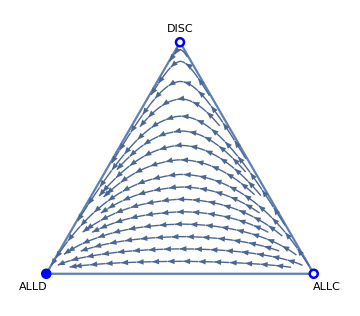

```mathematica
imageSJE0=Show[vlabels,ternplot,dots, ImageSize->Medium,Frame->False,PlotRangePadding->.1]
```

```mathematica
allimages=GraphicsGrid[{{imageSJE0,imageSJTol,imageSJStrict},{imageSSE0,imageSSTol,imageSSStrict},{imageSCE0,imageSCTol,imageSCStrict},{imageSHE0,imageSHTol,imageSHStrict}}]
```

Part::partw: Part 11 of {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}} does not exist.

Part::partd: Part specification {{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→0.775173},{fy→0,fx→1.01058×10^-10},{fy→0,fx→0},{fy→0,fx→0},{fy→0,fx→-4.88467×10^-10-4.77121×10^-10 ⅈ},{fy→0.643974,fx→0},{fy→0.697509,fx→-0.0996265}}⟦11⟧⟦2,2⟧ is longer than depth of object.

-Graphics-

```mathematica
Export["allimages.pdf",allimages];
```